```mathematica
ClearAll[Δ,corr,reduce,allgraphs]
SetAttributes[Δ,Orderless];

corr[{a_,b_}]:=Δ[a,b];
corr[{a_,b__}]:=corr[{a,b}]=Sum[corr[{a,List[b][[i]]}] corr[Flatten@{List[b][[;;i-1]],List[b][[i+1;;]]}],{i,1,Length[List[b]]}];

reduce[permutations_][graphs_List]/;Length[graphs]==1:={{First[graphs],1}};
reduce[permutations_][graphs_List]:=Map[MapAt[First,1],Tally[(#/. permutations)&/@graphs,ContainsAny],{1}]
```

```mathematica
allgraphs[n_List]/;OddQ[Sum[i n[[i]],{i,1,Length[n]}]]:={}
allgraphs[{2,0...}]={{{1<->2},2}};
allgraphs[n_List]:=Block[{permutations,gathered,removeiso,coeff},permutations=Dispatch[Thread/@Thread[ConstantArray[Range[n[[1]]+1,Total[n]],(Total[n]-n[[1]])!]->Permutations[Range[n[[1]]+1,Total[n]]]]/. Rule[a_,a_]->Nothing];
gathered=GatherBy[Select[{Expand[corr[Flatten[Table[ConstantArray[Total[n[[;;i-1]]]+j+1,i],{i,1,Length[n]},{j,0,n[[i]]-1}]]]]/. Plus->Sequence},WeaklyConnectedGraphQ[Graph[{#}/. {Times[a_Integer,g__]:>g,Times->Sequence}/. Power[a_,b_]:>Sequence@@ConstantArray[a,b]/. Δ->UndirectedEdge]]&],If[Head[First[#]]===Integer,First[#],1]&];
coeff=Map[If[Head[#[[1,1]]]===Integer,#[[1,1]],1]&,gathered];
removeiso=reduce[permutations]/@(Map[Sequence@@{#/. Times->Δ/.  Power[a_,b_]:>Sequence@@ConstantArray[a,b]}&,(gathered/coeff),{2}]);
Flatten[Table[Map[{(List@@#[[1]])/. Δ->UndirectedEdge,Apply[Times,Rest[n]!] Apply[Times,(Range[Length[n]]!)^n]/(#[[2]] coeff[[j]])}&,removeiso[[j]],{1}],{j,1,Length[coeff]}],1]]
```

```mathematica
allgraphsplot[n_]:=Graph[First[#],PlotLabel->Last[#],VertexLabels->Thread[Range[n[[1]]]->Range[n[[1]]]]]&/@allgraphs[n]
```

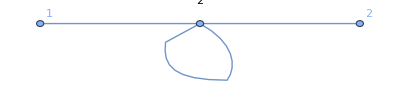

```mathematica
allgraphsplot[{2,0,0,1}]
```

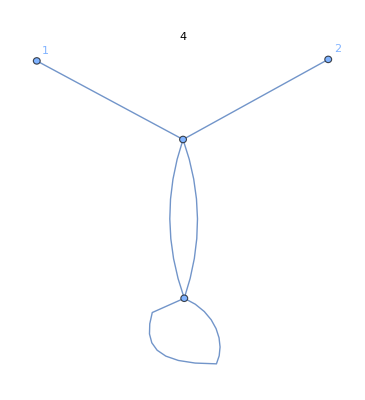
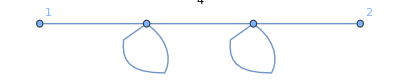
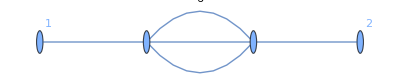

```mathematica
allgraphsplot[{2,0,0,2}]
```

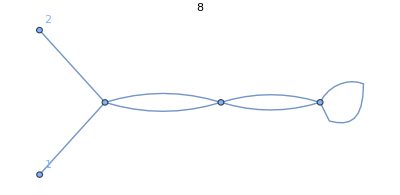
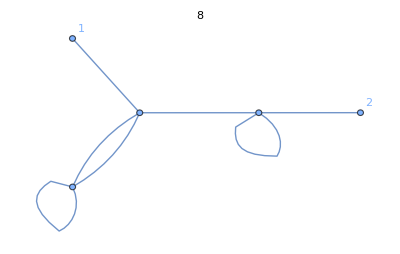
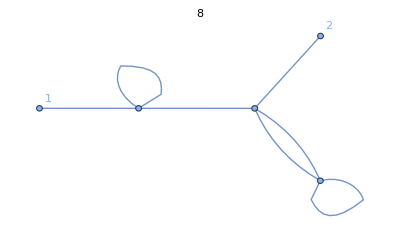
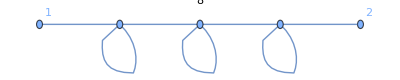
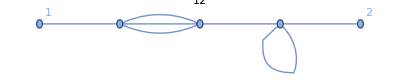
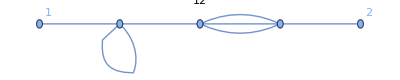
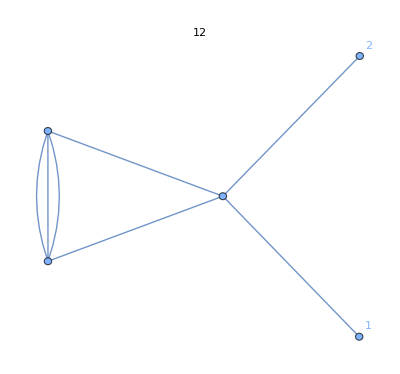
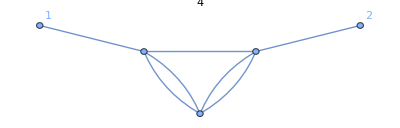

```mathematica
allgraphsplot[{2,0,0,3}]
```

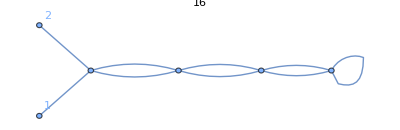
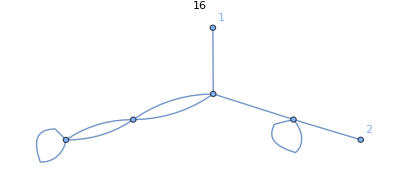
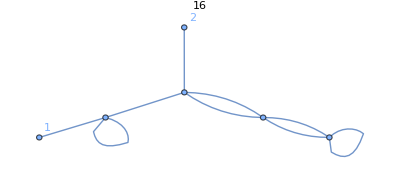
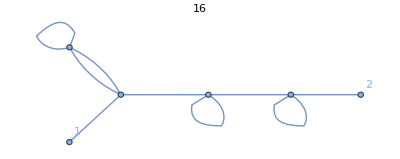
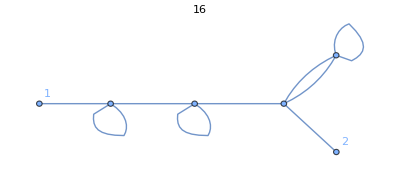
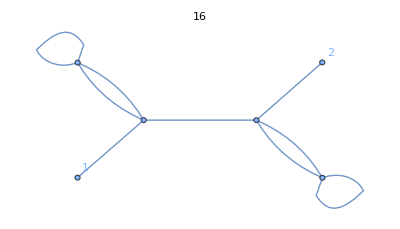
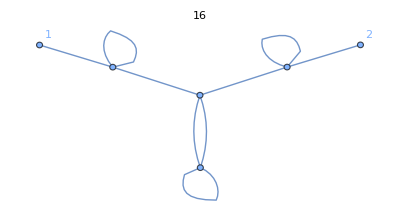
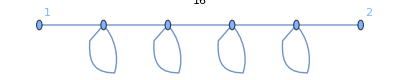

```mathematica
allgraphsplot[{2,0,0,4}]
```

```mathematica
allgraphsplot[{2,0,0,4}][[{14,15, 16, 20, 21, 22, 23, 28, 29, 30, 33, 34, 35, 36, 37, 38, 39}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Length[allgraphs[{2,0,0,4}]]
```

39

```mathematica
allgraphs[{2,0,0,4}]
```

{{{1<->6,2<->6,3<->5,3<->5,3<->6,3<->6,4<->4,4<->5,4<->5},16},{{1<->6,2<->4,3<->5,3<->5,3<->6,3<->6,4<->4,4<->6,5<->5},16},{{1<->4,2<->6,3<->5,3<->5,3<->6,3<->6,4<->4,4<->6,5<->5},16},{{1<->6,2<->5,3<->3,3<->6,3<->6,4<->4,4<->5,4<->6,5<->5},16},{{1<->5,2<->6,3<->3,3<->6,3<->6,4<->4,4<->5,4<->6,5<->5},16},{{1<->6,2<->4,3<->3,3<->6,3<->6,4<->5,4<->5,4<->6,5<->5},16},{{1<->5,2<->4,3<->3,3<->6,3<->6,4<->4,4<->6,5<->5,5<->6},16},{{1<->6,2<->5,3<->3,3<->4,3<->6,4<->4,4<->5,5<->5,6<->6},16},{{1<->6,2<->5,3<->5,3<->6,3<->6,3<->6,4<->4,4<->5,4<->5},24},{{1<->5,2<->6,3<->5,3<->6,3<->6,3<->6,4<->4,4<->5,4<->5},24},{{1<->6,2<->5,3<->4,3<->6,3<->6,3<->6,4<->4,4<->5,5<->5},24},{{1<->5,2<->6,3<->4,3<->6,3<->6,3<->6,4<->4,4<->5,5<->5},24},{{1<->5,2<->4,3<->5,3<->6,3<->6,3<->6,4<->4,4<->6,5<->5},24},{{1<->6,2<->6,3<->4,3<->5,3<->6,3<->6,4<->5,4<->5,4<->5},24},{{1<->6,2<->6,3<->5,3<->5,3<->5,3<->6,4<->4,4<->5,4<->6},12},{{1<->5,2<->4,3<->5,3<->6,3<->6,3<->6,4<->5,4<->5,4<->6},12},{{1<->5,2<->4,3<->4,3<->6,3<->6,3<->6,4<->5,4<->6,5<->5},24},{{1<->4,2<->5,3<->4,3<->6,3<->6,3<->6,4<->5,4<->6,5<->5},24},{{1<->6,2<->5,3<->4,3<->6,3<->6,3<->6,4<->5,4<->5,4<->5},36},{{1<->6,2<->5,3<->5,3<->5,3<->6,3<->6,4<->4,4<->5,4<->6},8},{{1<->6,2<->4,3<->5,3<->5,3<->6,3<->6,4<->5,4<->5,4<->6},8},{{1<->6,2<->6,3<->4,3<->5,3<->6,3<->6,4<->4,4<->5,5<->5},16},{{1<->6,2<->6,3<->4,3<->5,3<->5,3<->6,4<->4,4<->6,5<->5},8},{{1<->6,2<->5,3<->4,3<->5,3<->6,3<->6,4<->4,4<->6,5<->5},8},{{1<->5,2<->6,3<->4,3<->5,3<->6,3<->6,4<->4,4<->6,5<->5},8},{{1<->6,2<->5,3<->4,3<->4,3<->6,3<->6,4<->5,4<->6,5<->5},8},{{1<->5,2<->6,3<->4,3<->4,3<->6,3<->6,4<->5,4<->6,5<->5},8},{{1<->6,2<->6,3<->3,3<->5,3<->6,4<->4,4<->5,4<->6,5<->5},16},{{1<->6,2<->3,3<->5,3<->6,3<->6,4<->4,4<->5,4<->6,5<->5},8},{{1<->6,2<->3,3<->4,3<->6,3<->6,4<->5,4<->5,4<->6,5<->5},8},{{1<->6,2<->5,3<->3,3<->4,3<->6,4<->4,4<->6,5<->5,5<->6},16},{{1<->5,2<->6,3<->3,3<->4,3<->6,4<->4,4<->6,5<->5,5<->6},16},{{1<->6,2<->6,3<->4,3<->5,3<->5,3<->6,4<->5,4<->5,4<->6},8},{{1<->6,2<->5,3<->4,3<->5,3<->6,3<->6,4<->5,4<->5,4<->6},4},{{1<->6,2<->6,3<->4,3<->4,3<->5,3<->6,4<->5,4<->6,5<->5},8},{{1<->6,2<->4,3<->4,3<->5,3<->6,3<->6,4<->5,4<->6,5<->5},4},{{1<->4,2<->6,3<->4,3<->5,3<->6,3<->6,4<->5,4<->6,5<->5},4},{{1<->6,2<->5,3<->3,3<->5,3<->6,4<->4,4<->5,4<->6,5<->6},8},{{1<->6,2<->5,3<->4,3<->4,3<->5,3<->6,4<->5,4<->6,5<->6},4}}

```mathematica
allPossibleEdges[n_]:=Subsets[Range[n],{2}]/. {i_,j_}:>i<->j
multiplicityVector[edges_,n_]:=With[{counts=Counts[edges],allEdges=allPossibleEdges[n]},Lookup[counts,allEdges,0]]
vectors=allgraphs[{2,0,0,4}]/. {edges_,_}:>multiplicityVector[edges,6]
```

{{0,0,0,0,1,0,0,0,1,0,2,2,2,0,0},{0,0,0,0,1,0,1,0,0,0,2,2,0,1,0},{0,0,1,0,0,0,0,0,1,0,2,2,0,1,0},{0,0,0,0,1,0,0,1,0,0,0,2,1,1,0},{0,0,0,1,0,0,0,0,1,0,0,2,1,1,0},{0,0,0,0,1,0,1,0,0,0,0,2,2,1,0},{0,0,0,1,0,0,1,0,0,0,0,2,0,1,1},{0,0,0,0,1,0,0,1,0,1,0,1,1,0,0},{0,0,0,0,1,0,0,1,0,0,1,3,2,0,0},{0,0,0,1,0,0,0,0,1,0,1,3,2,0,0},{0,0,0,0,1,0,0,1,0,1,0,3,1,0,0},{0,0,0,1,0,0,0,0,1,1,0,3,1,0,0},{0,0,0,1,0,0,1,0,0,0,1,3,0,1,0},{0,0,0,0,1,0,0,0,1,1,1,2,3,0,0},{0,0,0,0,1,0,0,0,1,0,3,1,1,1,0},{0,0,0,1,0,0,1,0,0,0,1,3,2,1,0},{0,0,0,1,0,0,1,0,0,1,0,3,1,1,0},{0,0,1,0,0,0,0,1,0,1,0,3,1,1,0},{0,0,0,0,1,0,0,1,0,1,0,3,3,0,0},{0,0,0,0,1,0,0,1,0,0,2,2,1,1,0},{0,0,0,0,1,0,1,0,0,0,2,2,2,1,0},{0,0,0,0,1,0,0,0,1,1,1,2,1,0,0},{0,0,0,0,1,0,0,0,1,1,2,1,0,1,0},{0,0,0,0,1,0,0,1,0,1,1,2,0,1,0},{0,0,0,1,0,0,0,0,1,1,1,2,0,1,0},{0,0,0,0,1,0,0,1,0,2,0,2,1,1,0},{0,0,0,1,0,0,0,0,1,2,0,2,1,1,0},{0,0,0,0,1,0,0,0,1,0,1,1,1,1,0},{0,0,0,0,1,1,0,0,0,0,1,2,1,1,0},{0,0,0,0,1,1,0,0,0,1,0,2,2,1,0},{0,0,0,0,1,0,0,1,0,1,0,1,0,1,1},{0,0,0,1,0,0,0,0,1,1,0,1,0,1,1},{0,0,0,0,1,0,0,0,1,1,2,1,2,1,0},{0,0,0,0,1,0,0,1,0,1,1,2,2,1,0},{0,0,0,0,1,0,0,0,1,2,1,1,1,1,0},{0,0,0,0,1,0,1,0,0,1,1,2,1,1,0},{0,0,1,0,0,0,0,0,1,1,1,2,1,1,0},{0,0,0,0,1,0,0,1,0,0,1,1,1,1,1},{0,0,0,0,1,0,0,1,0,2,1,1,1,1,1}}

```mathematica
(*Step 1:generate multiplicity vectors*)allPossibleEdges[n_]:=Subsets[Range[n],{2}]/. {i_,j_}:>i<->j
multiplicityVector[edges_,n_]:=With[{counts=Counts[edges],allEdges=allPossibleEdges[n]},Lookup[counts,allEdges,0]]
vectors=allgraphs[{2,0,0,4}]/. {edges_,_}:>multiplicityVector[edges,6];
(*Step 2:sort each vector*)
sortedVectors=Sort/@vectors;
(*Step 3:tally them*)
tallied=Tally[sortedVectors];
(*Step 4:number of unique multiplicity patterns*)
numUnique=Length[tallied]
```

17

```mathematica
tallied
```

{{{0,0,0,0,0,0,0,0,0,0,1,1,2,2,2},1},{{0,0,0,0,0,0,0,0,0,0,1,1,1,2,2},3},{{0,0,0,0,0,0,0,0,0,0,1,1,1,1,2},3},{{0,0,0,0,0,0,0,0,0,0,1,1,1,1,1},1},{{0,0,0,0,0,0,0,0,0,0,1,1,1,2,3},2},{{0,0,0,0,0,0,0,0,0,0,1,1,1,1,3},3},{{0,0,0,0,0,0,0,0,0,1,1,1,1,2,3},2},{{0,0,0,0,0,0,0,0,0,1,1,1,1,1,3},3},{{0,0,0,0,0,0,0,0,0,0,1,1,1,3,3},1},{{0,0,0,0,0,0,0,0,0,1,1,1,1,2,2},4},{{0,0,0,0,0,0,0,0,0,1,1,1,2,2,2},1},{{0,0,0,0,0,0,0,0,0,1,1,1,1,1,2},5},{{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},3},{{0,0,0,0,0,0,0,0,1,1,1,1,1,2,2},2},{{0,0,0,0,0,0,0,0,1,1,1,1,1,1,2},3},{{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1},1},{{0,0,0,0,0,0,0,1,1,1,1,1,1,1,2},1}}

```mathematica
irreducibleQ[edges_]:=Module[{g,verts,test},g=Graph[edges,VertexLabels->None];
test[e_]:=Module[{g2,degs,keep},(*remove one edge*)g2=EdgeDelete[g,e];
(*find vertices of degree 1*)degs=VertexDegree[g2];
keep=VertexList[g2][[Flatten[Position[degs,_?(#>1&)]]]];
If[keep==={},True,ConnectedGraphQ[Subgraph[g2,keep]]]];
AllTrue[EdgeList[g],test]]
irreducibles=Select[allgraphs[{2,0,0,4}],irreducibleQ[First[#]]&];
Length[irreducibles ]
```

18

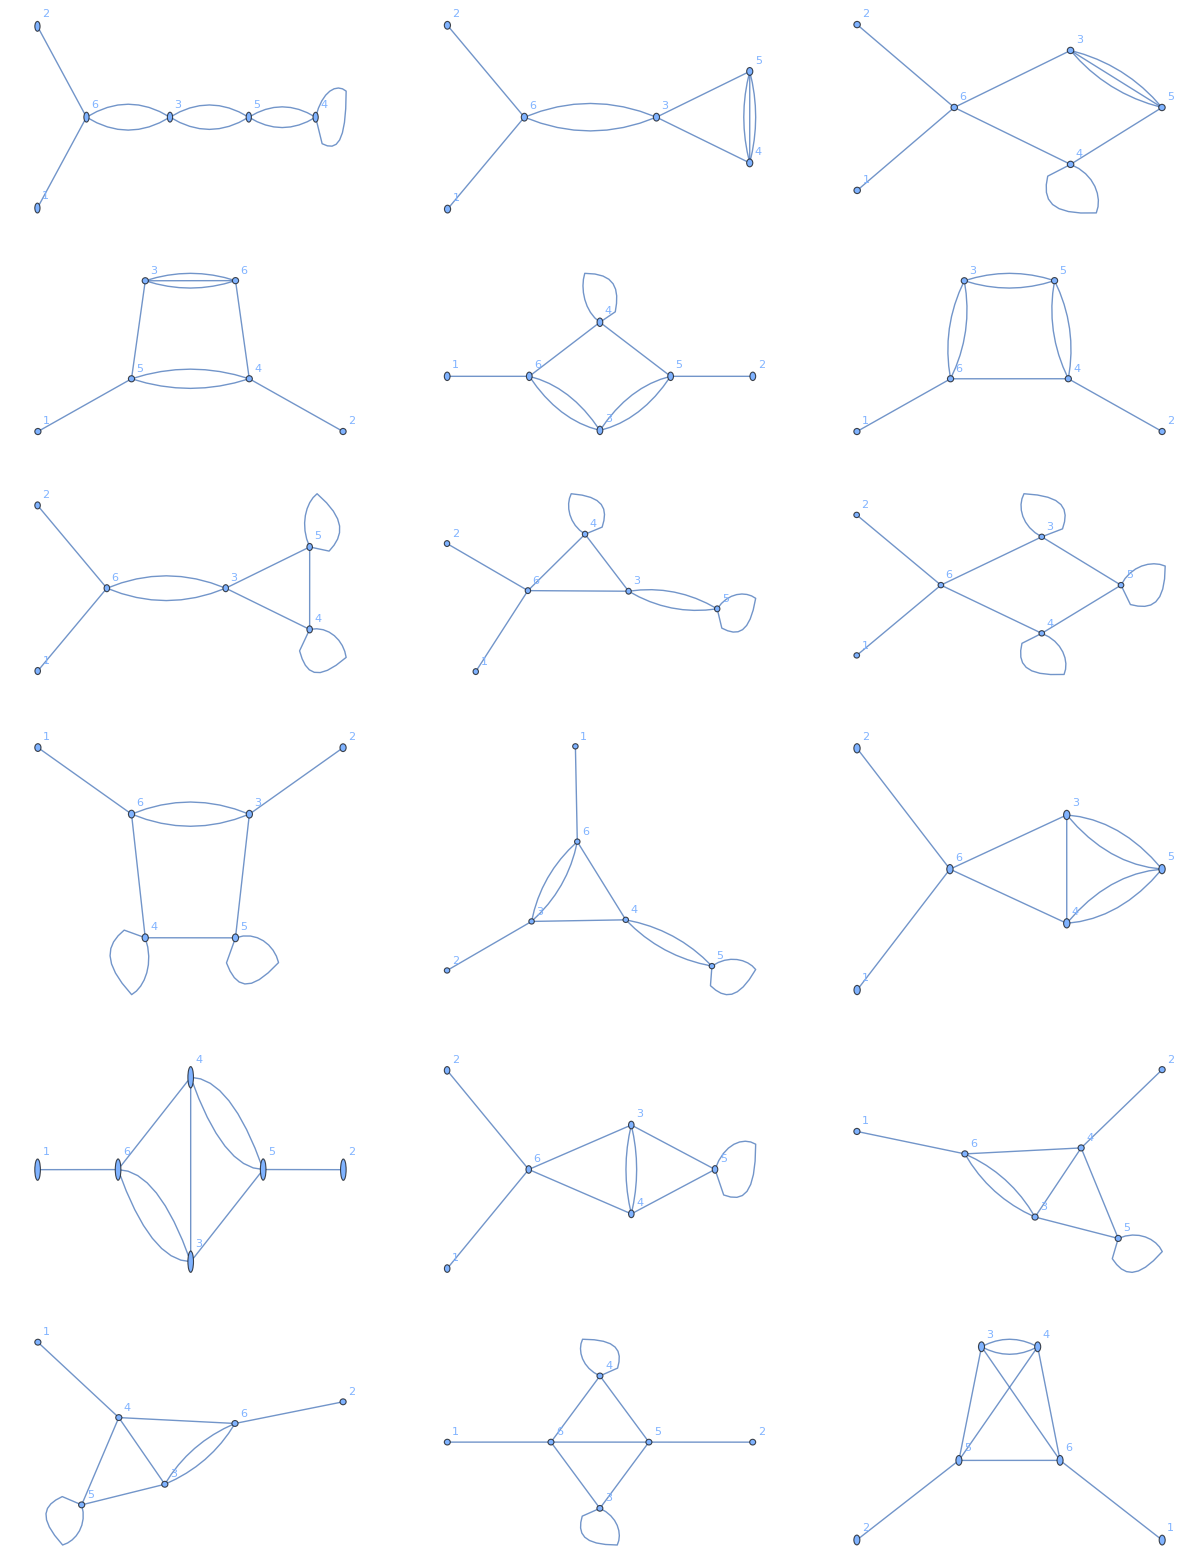

```mathematica
(*irreducibility check as defined before*)irreducibleQ[edges_]:=Module[{g,test},g=Graph[edges];
test[e_]:=Module[{g2,degs,keep},g2=EdgeDelete[g,e];
(*keep only vertices with degree>1*)degs=VertexDegree[g2];
keep=VertexList[g2][[Flatten[Position[degs,_?(#>1&)]]]];
If[keep==={},True,ConnectedGraphQ[Subgraph[g2,keep]]]];
AllTrue[EdgeList[g],test]];

(*extract only irreducible graphs*)
irreducibleEdges=Select[allgraphs[{2,0,0,4}],irreducibleQ[First[#]]&][[All,1]];

(*plot them all in a grid*)
GraphicsGrid[Partition[Graph[#,VertexLabels->"Name"]&/@irreducibleEdges,UpTo[3]]]
```

```mathematica
(*----helper:all possible edges----*)allPossibleEdges[n_]:=Subsets[Range[n],{2}]/. {i_,j_}:>i<->j

(*----multiplicity vector (zeros if absent)----*)
multiplicityVector[edges_,n_]:=With[{counts=Counts[edges],allEdges=allPossibleEdges[n]},Lookup[counts,allEdges,0]]

(*----irreducibility check----*)
irreducibleQ[edges_]:=Module[{g,test},g=Graph[edges];
test[e_]:=Module[{g2,degs,keep},g2=EdgeDelete[g,e];
degs=VertexDegree[g2];
keep=VertexList[g2][[Flatten[Position[degs,_?(#>1&)]]]];
If[keep==={},True,ConnectedGraphQ[Subgraph[g2,keep]]]];
AllTrue[EdgeList[g],test]];

(*----get all irreducible graphs----*)
irreducibleEdges=Select[allgraphs[{2,0,0,4}],irreducibleQ[First[#]]&][[All,1]];

(*----compute sorted multiplicity vectors----*)
irreducibleVectors=Sort/@(multiplicityVector[#,6]&/@irreducibleEdges);

(*----tally unique patterns----*)
uniqueIrreduciblePatterns=Tally[irreducibleVectors]
numUniqueIrreducible=Length[uniqueIrreduciblePatterns]
```

{{{0,0,0,0,0,0,0,0,0,0,1,1,2,2,2},1},{{0,0,0,0,0,0,0,0,0,1,1,1,1,2,3},2},{{0,0,0,0,0,0,0,0,0,1,1,1,1,1,3},1},{{0,0,0,0,0,0,0,0,0,1,1,1,1,2,2},2},{{0,0,0,0,0,0,0,0,0,1,1,1,2,2,2},1},{{0,0,0,0,0,0,0,0,0,1,1,1,1,1,2},3},{{0,0,0,0,0,0,0,0,0,1,1,1,1,1,1},1},{{0,0,0,0,0,0,0,0,1,1,1,1,1,2,2},2},{{0,0,0,0,0,0,0,0,1,1,1,1,1,1,2},3},{{0,0,0,0,0,0,0,0,1,1,1,1,1,1,1},1},{{0,0,0,0,0,0,0,1,1,1,1,1,1,1,2},1}}

11

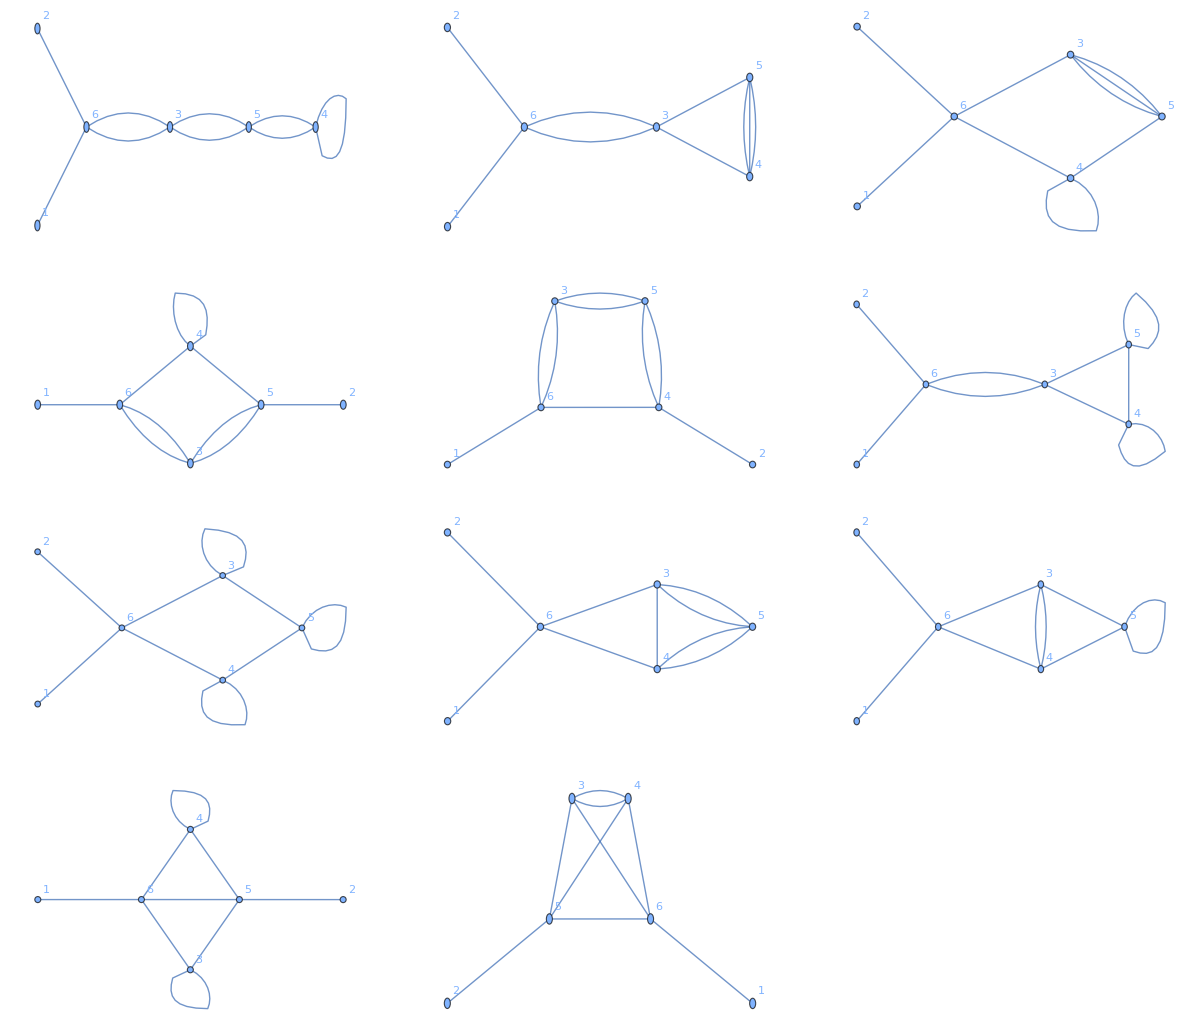

```mathematica
(*----helper:all possible edges----*)allPossibleEdges[n_]:=Subsets[Range[n],{2}]/. {i_,j_}:>i<->j

(*----multiplicity vector (zeros if absent)----*)
multiplicityVector[edges_,n_]:=With[{counts=Counts[edges],allEdges=allPossibleEdges[n]},Lookup[counts,allEdges,0]]

(*----irreducibility check----*)
irreducibleQ[edges_]:=Module[{g,test},g=Graph[edges];
test[e_]:=Module[{g2,degs,keep},g2=EdgeDelete[g,e];
degs=VertexDegree[g2];
keep=VertexList[g2][[Flatten[Position[degs,_?(#>1&)]]]];
If[keep==={},True,ConnectedGraphQ[Subgraph[g2,keep]]]];
AllTrue[EdgeList[g],test]];

(*----get irreducible graphs----*)
irreducibleEdges=Select[allgraphs[{2,0,0,4}],irreducibleQ[First[#]]&][[All,1]];

(*----compute sorted multiplicity vectors----*)
irreducibleVectors=Sort/@(multiplicityVector[#,6]&/@irreducibleEdges);

(*----pair edges with their multiplicity pattern----*)
paired=Transpose[{irreducibleEdges,irreducibleVectors}];

(*----representative of each unique multiplicity pattern----*)
uniqueReps=Values@GroupBy[paired,Last->First,First];

(*----plot them in a grid----*)
GraphicsGrid[Partition[Graph[#,VertexLabels->"Name"]&/@uniqueReps,UpTo[3]]]
```

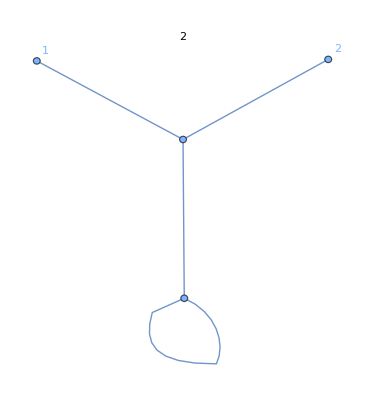
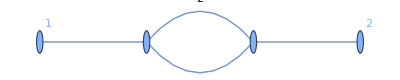

```mathematica
allgraphsplot[{2,0,2}]
```

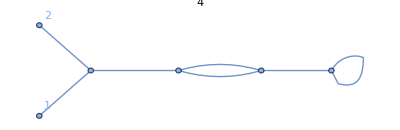
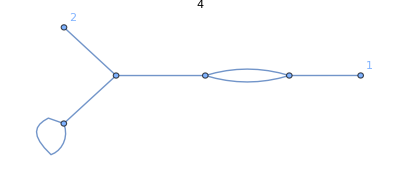
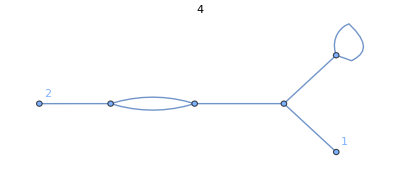
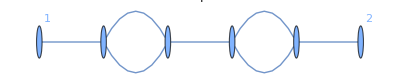
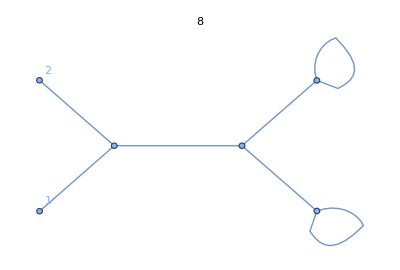
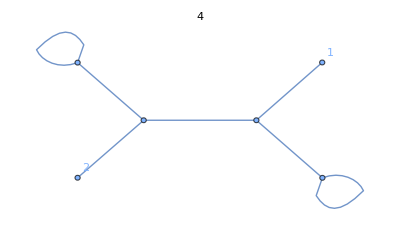
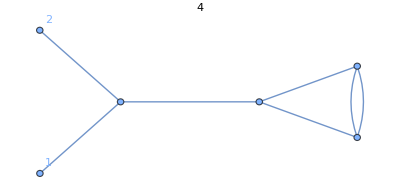
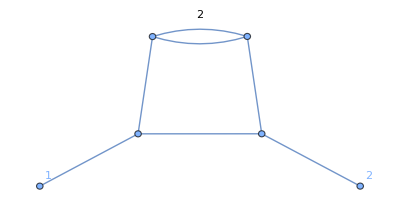

```mathematica
allgraphsplot[{2,0,4}]
```